## July 2020 - Revised calculations for ^135 Pr

## Computing the Contour Plots and the Triaxial Potential for the nucleus

### Constants

```mathematica
j13=13/2;
j11=11/2;
spinValue=19/2;
theta1=-30*π/180;
theta2=-70*π/180;
```

### Formulas

```mathematica
j1[j_,θ_]:=j*Cos[θ];
j2[j_,θ_]:=j*Sin[θ];
Afct[I_,a1_,a2_,j_,θ_]:=a2*(1-j2[j,θ]/I)-a1;
ufct[I_,a1_,a2_,a3_,j_,θ_]:=(a3-a1)/Afct[I,a1,a2,j,θ];
v0fct[I_,a1_,a2_,j_,θ_]:=-(a1*j1[j,θ])/Afct[I,a1,a2,j,θ];
kfct[I_,a1_,a2_,a3_,j_,θ_]:=Sqrt[ufct[I,a1,a2,a3,j,θ]];
IF[moi_]:=1/(2*moi);
```

### Parametric constants k

```mathematica
k9010030=kfct[spinValue,IF[90],IF[100],IF[30],j13,theta1];
k891248=kfct[spinValue,IF[89],IF[12],IF[48],j11,-71*π/180];
k354020=kfct[spinValue,IF[35],IF[40],IF[20],j13,theta2];
k152040=kfct[spinValue,IF[10],IF[20],IF[40],j13,theta2];
k401020=kfct[spinValue,IF[40],IF[10],IF[20],j13,theta2];
kValues={k9010030,k891248,k354020,k152040,k401020};
```

### Testing the numerical parameter consistency with Raduta’s values

```mathematica
Do[Print[N[kValues[[i]]]],{i,1,Length[kValues]}]
```

3.10165

0.285536

1.30919

2.04965

0.423646

### Generate the q-values for plotting the potential

```mathematica
kTest=0.3;
qValues=Table[q,{q,-8,8,0.1}];
fiValues[q_,k_]:=Table[JacobiAmplitude[q[[i]],k],{i,1,Length[q]}];
```

### Jacobi Functions - Functions for the elliptic variables

```mathematica
fiVar[q_,k_]:=JacobiAmplitude[q,k];
```

### Potential expression

```mathematica
vRotor[I_,q_,k_,v_]:=(I(I+1)k^2+v^2)Sin[fiVar[q,k]]^2+(2I+1)v*Cos[fiVar[q,k]]*√(1-k^2 Sin[fiVar[q,k]]^2);
```

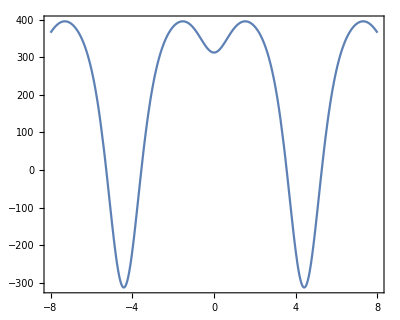

```mathematica
Plot[vRotor[45/2,q,kfct[45/2,IF[20],IF[100],IF[40],13/2,30*π/180],v0fct[45/2,IF[20],IF[100],13/2,30*π/180]],{q,-8,8},AspectRatio->0.8,Frame->True,Axes->False]
```

### Jacobi Functions

```mathematica
Afct[spinValue,IF[90],IF[100],6.5,theta1]
```

0.00115497